Lawrence Lee

北京理工大学

2020.10.31

可能用到的程序包

<< MaTeX`;
<< Notation`;
<< MATLink`;
OpenMATLAB[];
<< GroupTheory`;
<< Quantum`Notation`;
SetQuantumAliases[];

```mathematica
<<MaTeX`
```

可能用到的表达式

```mathematica
<<Notation`
Symbolize[Subscript[A, x]]
Symbolize[Subscript[A, y]]
Symbolize[Subscript[ϕ, ph]]
Symbolize[Subscript[f, x]]
Symbolize[Subscript[f, y]]
Symbolize[Subscript[f, 3]]
Symbolize[Subscript[pts, 0]]
```

```mathematica
ToExpression["\\sqrt{\\frac{x}{y}}",TeXForm]
```

√(x/y)

提高MMA运算速度

["10 Tips for Writing Fast Mathematica Code"](https://blog.wolfram.com/2011/12/07/10-tips-for-writing-fast-mathematica-code/)

["Performance tuning in Mathematica?"](https://mathematica.stackexchange.com/questions/29349/performance-tuning-in-mathematica)

## 1. 涡旋

#### 1. 平面光

转动速度

```mathematica
b=5
```

5

```mathematica
p4=Graphics3D[{Black,Tube[{{-10,0,0},{10,0,0}},0.015]}];
```

```mathematica
Table[Show[{p4,ParametricPlot3D[{{a,u Sin[t+b*a],u Cos[t+b*a]},{1+a,u Sin[t+b*a],u Cos[t+b*a]},{2+a,u Sin[t+b*a],u Cos[t+b*a]}},{t,0,2π},{u,0,1},PlotStyle->Directive[Red,Opacity[0.8],Specularity[White,20]],Axes->None,Boxed->None,PlotPoints->100,AxesEdge->None]},Boxed->False,PlotRange->{{0.4,2.9},{-1,1},{-1,1}}],{a,0,1,0.05}]//Export["非涡旋光.gif",#]&//SystemOpen
```

#### 2. 涡旋光

```mathematica
Table[Show[{p4,ParametricPlot3D[{{t+a,u*Sin[t+b*a],u* Cos[t+b*a]}},{t,-2π,2π},{u,0,1},PlotStyle->Directive[Red,Opacity[0.8],Specularity[White,20]],Axes->None,Boxed->None,PlotPoints->100,AxesEdge->None]},Boxed->False,PlotRange->{{-π,π},{-1,1},{-1,1}}],{a,0,1,0.05}]//Export["涡旋光=1.gif",#]&//SystemOpen
```

```mathematica
Table[Show[{p4,ParametricPlot3D[{{t+a,u*Sin[t+b*a],u* Cos[t+b*a]},{t+a,u*Sin[t+π+b*a],u* Cos[t+π+b*a]}},{t,-2π,2π},{u,0,1},PlotStyle->Directive[Red,Opacity[0.8],Specularity[White,20]],Axes->None,Boxed->None,PlotPoints->100,AxesEdge->None]},Boxed->False,PlotRange->{{-π,π},{-1,1},{-1,1}}],{a,0,1,0.05}]//Export["涡旋光=2.gif",#]&//SystemOpen
```

```mathematica
Table[Show[{p4,ParametricPlot3D[{{t+a,u*Sin[t+b*a],u* Cos[t+b*a]},{t+a,u*Sin[t+2 π/3+b*a],u* Cos[t+2 π/3+b*a]},{t+a,u*Sin[t+4 π/3+b*a],u* Cos[t+4 π/3+b*a]}},{t,-2π,2π},{u,0,1},PlotStyle->Directive[Red,Opacity[0.8],Specularity[White,20]],Axes->None,Boxed->None,PlotPoints->100,AxesEdge->None]},Boxed->False,PlotRange->{{-π,π},{-1,1},{-1,1}}],{a,0,1,0.05}]//Export["涡旋光=3.gif",#]&//SystemOpen
```

```mathematica
Table[Show[{p4,ParametricPlot3D[{{t+a,u*Sin[t+b*a],u* Cos[t+b*a]},{t+a,u*Sin[t+π/2+b*a],u* Cos[t+π/2+b*a]},{t+a,u*Sin[t+π+b*a],u* Cos[t+π+b*a]},{t+a,u*Sin[t+(3π)/2+b*a],u* Cos[t+(3π)/2+b*a]}},{t,-2π,2π},{u,0,1},PlotStyle->Directive[Red,Opacity[0.8],Specularity[White,20]],Axes->None,Boxed->None,PlotPoints->100,AxesEdge->None]},Boxed->False,PlotRange->{{-π,π},{-1,1},{-1,1}}],{a,0,1,0.05}]//Export["涡旋光=4.gif",#]&//SystemOpen
```

#### 工具

```mathematica
Hyperlink["",""]//Print
```

```mathematica
Rasterize[,RasterSize->1000]//Print
```

```mathematica
HoldForm[ℓ=4]//MaTeX[#,Magnification->2]&//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

```mathematica
(%//AbsoluteTiming)⟦1⟧*1000
```

## 2. 偏振

```mathematica
f[Ax_,Ay_,dphase_]:=
Module[{k=Pi,w=2Pi,fx,fy,result,f3,pts0},
fx=Function[t,Ay Cos[w t-k 0],Listable];
fy=Function[t,Ay Cos[w t-k 0+dphase],Listable];
f3[t_]:=Table[Arrow@Tube[{{z,0,0},{z,Ay Cos[w t- k z],Ay Cos[w t-k z+dphase]}}],{z,0,2,0.05}];
pts0=Table[{0,Ay Cos[w t- k 0],Ay Cos[w t-k 0+dphase]},{t,0,1,0.01}];
result=Transpose[Through[{fx,fy}[Range[0,1,0.01]]]];DynamicModule[{i=1},Column[{{Slider[Dynamic[i],{1,100,1}],Dynamic[i]},Row[{Graphics[{{Red,Point[result]},Point[{{0,0}}],{Arrowheads[0.1],Arrow[result[[;;25]]]},{Dynamic@Arrow[{{0,0},result[[i]]}]},{EdgeForm[Black],Opacity[0],Rectangle[{-Ax,-Ay},{Ax,Ay}]}},ImageSize->200],Graphics3D[{Arrowheads[0.02],Blue,f3[Dynamic[i/100]],{Red,Point[pts0]}},ImageSize->500,BoxRatios->{3, 1, 1},Boxed->False,ViewPoint->{1.152245850052173,-3.1807506093481455,0.07179876161150522}]}]}]]]
```

```mathematica
f[1,1,π/2]
```

#### 工具

```mathematica
Hyperlink["",""]//Print
```

```mathematica
Rasterize[,RasterSize->1000]//Print
```

```mathematica
HoldForm[]//MaTeX[#,Magnification->2]&//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

```mathematica
(%//AbsoluteTiming)⟦1⟧*1000
```

## 3. 偏振环

```mathematica
p1=Graphics3D[Table[Tube[{{10Cos[(a)*0.01π],10Sin[(a)*0.01π],0},{10Cos[(a+1)*0.01π],10Sin[(a+1)*0.01π],0}}],{a,0,200}]];
p2=Graphics3D[{Table[{Arrowheads[0.01],Arrow[{{10Cos[t],10Sin[t],0},{10Cos[t],10Sin[t],5Cos[3t]}}]},{t,0,2π,0.02}],Boxed->False}];
Table[Show[{p1,Graphics3D[{Table[{Arrowheads[0.01],Arrow[{{10Cos[t+a],10Sin[t+a],0},{10Cos[t+a],10Sin[t+a],5*Cos[3t]}}]},{t,0,2π,0.02}],Boxed->False}]},Boxed->False],{a,0,2π,0.1π}]//Export["1.gif",#]&//SystemOpen[DirectoryName[AbsoluteFileName[#]]]&
```

#### 工具

```mathematica
Hyperlink["",""]//Print
```

```mathematica
Rasterize[,RasterSize->1000]//Print
```

```mathematica
HoldForm[]//MaTeX[#,Magnification->2]&//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

```mathematica
(%//AbsoluteTiming)⟦1⟧*1000
```

## 4.

#### 工具

```mathematica
Hyperlink["",""]//Print
```

```mathematica
Rasterize[,RasterSize->1000]//Print
```

```mathematica
HoldForm[]//MaTeX[#,Magnification->2]&//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

```mathematica
(%//AbsoluteTiming)⟦1⟧*1000
```

## 技巧

### 1. Flatten

-Graphics-

用TreeForm辅助，看应该把哪两层放在一起

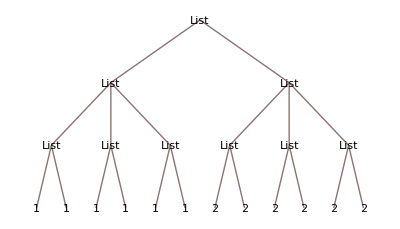

{{1,1,1},{2,2,2}}

0.0027

```mathematica
{{{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2}}}//TreeForm
Flatten[{{{1},{1},{1}},{{2},{2},{2}}},{{1},{2,3}}]
a=(%//AbsoluteTiming)⟦1⟧*1000
```

```mathematica
Flatten[{{1},{1},{1}},2]
Flatten[#,2]&/@{{{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2}}}
b=(%//AbsoluteTiming)⟦1⟧*1000
```

{1,1,1}

{{1,1,1,1,1,1},{2,2,2,2,2,2}}

0.0023